```mathematica
<<Local`QFTToolKit`
DefineTensorShortcuts[{{Q},1},{{σ},4}]
QCDBaseIndices
DefineDottedIndices
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3,4,5,6,7,8}},{color,{1,2,3}},{flavor,{1,2,3,4,5,6}},{family,{1,2,3}}}

```mathematica
DefineTensorShortcuts[{{η,t,δ,ε,λ,D,F,U,"E",H,g,τ,v},1},
{{y,U,u,ψ,V,h},2},
{{σ,λ,T},3}
]
```

Lecture 26 Sept 2011 notes

```mathematica
PR1["How to make SUSY Lagrangian gauge invariant, i.e., under transform: ",
tmp=ϕ->E[I Q.Λ].ϕ," where we can expand ",
ϕ->A + θ.ψ+⋯,NL,
"If we modify the scalar kinetic term ",tmp1=(SuperDagger[ϕ].ϕ)[θ θ θ̄ θ̄]->(SuperDagger[ϕ].Exp[g Q.V].ϕ)[θ θ θ̄ θ̄],
" where vector superfield V ∈ Real, ",
tmpV=V->⋯+θ.σu[μ].θ̄.Ad[μ][x]+θ̄.θ̄.θ λ[x]+θ .θ.θ̄.λ̄+θ .θ.θ̄.θ̄.Dd[x],NL,
"If we convert the kinetic terms to use covariant derivatives ",
tmp=Subscript[ℒ, kinetic]->SuperDagger[xCovariantDu[A,μ]].xCovariantD[A,μ]+I ψ.σu[μ].xCovariantD[ψ̄,μ],
" where ", xCovariantDu[_,μ]->xPartialDu[_,μ]-I g Q Au[μ],
" results in potential ",tmp=Subscript[V, D^2]->(g g)/2(SuperDagger[A].Q.A)^2,
" and Lagrangian gauge term ",tmp=Subscript[ℒ, gauge]->√2 g SuperDagger[Ad[i]].Tudd[a,i,j].ψud[a,j].Au[a]


]
```

How to make SUSY Lagrangian gauge invariant, i.e., under transform: ϕ→ⅇ[ⅈ Q.Λ].ϕ where we can expand ϕ→A+⋯+θ.ψ
If we modify the scalar kinetic term (ϕ^†.ϕ)[θ^2 (θ̄)^2]→(ϕ^†.ⅇ^(g Q.V).ϕ)[θ^2 (θ̄)^2] where vector superfield V ∈ Real, V→⋯+θ.θ.θ̄.λ̄+θ.σ_μ^μ.θ̄.A_μ^μ[x]+θ.θ.θ̄.θ̄.D_x^x+θ̄.θ̄.θ λ[x]
If we convert the kinetic terms to use covariant derivatives ℒ_kinetic→((𝔇̲)^μ[A])^†.(𝔇̲)_μ[A]+ⅈ ψ.σ_μ^μ.(𝔇̲)_μ[ψ̄] where (𝔇̲)^μ[_]→-ⅈ g Q A_μ^μ+UnderBar[∂]^μ[_] results in potential V_(D^2)→1/2 g^2 (A^†.Q.A)^2 and Lagrangian gauge term ℒ_gauge→√2 g (A_i^i)^†.T_aij^aij.ψ_aj^aj.A_a^a

```mathematica
PR1["The non-abelian theory is straight forward: Replace ",Q-> Tudd[a,i,j].Q,
" which results in changes ",
{ℒ-> ϕd[i].Exp[g Vdd[i,j]].ϕd[j],
Subscript[V, D^2]->xSum[(g g)/2(SuperDagger[Ad[i]].Tudd[a,i,j].Ad[j])^2,{a}]
}," where {i,j} are color indices."
];
```

The non-abelian theory is straight forward: Replace Q→T_aij^aij.Q which results in changes {ℒ→ϕ_i^i.ⅇ^(g V_ij^ij).ϕ_j^j,V_(D^2)→UnderBar[∑]_{a}[1/2 g^2 ((A_i^i)^†.T_aij^aij.A_j^j)^2]} where {i,j} are color indices.

```mathematica
PR1["For the MSSM we have the super-fields: ",{Q,Uu[c],Du[c],L,Eu[c],Hd[u],Hd[d]},
" where the pattern for superfields is: ",
{ Q->q̃+θ.q, Hd[u_]->hd[u]+θ.T[h̃,{},{u}]},NL,
"This produces potential terms like: ",
(gd[3]^2/2).(SuperDagger[T[q̃,{},{i}]].λudd[a,i,j].T[q̃,{},{j}]+SuperDagger[T[ũ,{c,},{,i}]].(-SuperStar[λudd[a,i,j]]).T[ũ,{c,},{,j}]+
T[d̃,"ud",{c,i}].(-SuperStar[λudd[a,i,j]]).T[d̃,{c,},{,j}])^2
];
```

For the MSSM we have the super-fields: {Q,U_c^c,D_c^c,L,Eu[c],H_u^u,H_d^d} where the pattern for superfields is: {Q→θ.q+q̃,H_u_^u_→θ.(h̃)_u^u+h_u^u}
This produces potential terms like: (1/2 (g_3^3)^2).(((q̃)_i^i)^†.λ_aij^aij.(q̃)_j^j+((ũ)_ci^ci)^†.(-(λ_aij^aij)^*).(ũ)_cj^cj+(d̃)_ci^ci.(-(λ_aij^aij)^*).(d̃)_cj^cj)^2

```mathematica
PR1["What is Higgs potential? ",NL,
tmp=W->Q.yd[u].Uu[c].Hd[u]+
Q.yd[d].Du[c].Hd[d]+
L.yd[e].Eu[c].Hd[d]+
μ.Hd[u].Hd[d];
ColumnSumExp[tmp],Imply,
V[hd[u],hd[d]]->Abs[F]^2+D^2/2->μ(SuperDagger[hd[d]].hd[d]+SuperDagger[hd[u]].hd[u]),Imply,
Subscript[m, h]>0,NL,
"This adds gauge terms: ",
(SuperDagger[hd[u]].(τu[a]/2).hd[u]+SuperDagger[hd[d]].(τu[a]/2).hd[d] )^2," where ",
{hd[u]->{{hud["+",u]},{hud[0,u]}},hd[d]->{{hud[0,d]},{hud["-",d]}}}//MatrixForms,
NL,
"For VEV: ",{BraKet[hd[u]]->{{0},{vd[u]}},BraKet[hd[d]]->{{vd[d]},{0}}}//MatrixForms,Imply,
Vd[h]->μ(vd[u]^2+vd[d]^2)+g^2/8(-vd[u]^2+vd[d]^2)^2+g'^2/8(vd[u]^2-vd[d]^2)^2,NL,
"For MSSM before SUSY breaking V≥0, so EWS not broken. Since EWS breaking is observed how is it done? Possiblies (1) Break SUSY with super V_SUSY breaking, (2) SUSY with ",{vd[d],vd[u]}≠0
];
```

What is Higgs potential? 
W→∑[μ.H_u^u.H_d^d
L.y_e^e.Eu[c].H_d^d
Q.y_d^d.D_c^c.H_d^d
Q.y_u^u.U_c^c.H_u^u]
⇒ V[h_u^u,h_d^d]→D^2/2+Abs[F]^2→μ ((h_d^d)^†.h_d^d+(h_u^u)^†.h_u^u)
⇒ m_h>0
This adds gauge terms: ((h_d^d)^†.τ_a^a/2.h_d^d+(h_u^u)^†.τ_a^a/2.h_u^u)^2 where {h_u^u→(h_(+u)^(+u)
h_(0u)^(0u)),h_d^d→(h_(0d)^(0d)
h_-d^-d)}
For VEV: {⟨h_u^u⟩→(0
v_u^u),⟨h_d^d⟩→(v_d^d
0)}
⇒ Vd[h]→1/8 g^2 ((v_d^d)^2-(v_u^u)^2)^2+μ ((v_d^d)^2+(v_u^u)^2)+1/8 (-(v_d^d)^2+(v_u^u)^2)^2 (g')^2
For MSSM before SUSY breaking V≥0, so EWS not broken. Since EWS breaking is observed how is it done? Possiblies (1) Break SUSY with super V_SUSY breaking, (2) SUSY with {v_d^d,v_u^u}≠0

```mathematica
PR1["How to transition from SUSY[E≫1] to SUSY[E∼v] without breaking SUSY? Propose that: ",
tmp=W->X(λ.Hd[u].Hd[d]-M M)," where we get a potential ",Imply,
V[x,Hd[u],Hd[d]]->Abs[λ.hd[u].hd[d]-M M]^2+Abs[λ.X.hd[d]]^2+Abs[λ.X.hd[u]]^2," with h-VEV's ",Imply,
V[x,Hd[u],Hd[d]]->(λ vd[u]vd[u]-M M)^2+λ λ vd[x] (vd[u]^2+vd[d]^2)+(g g+g' g')/8(vd[u]^2-vd[d]^2),NL,
"For V->0: ",imply,{vd[d],vd[u]}->M
];
```

How to transition from SUSY[E≫1] to SUSY[E∼v] without breaking SUSY? Propose that: W→X (-M^2+λ.H_u^u.H_d^d) where we get a potential 
⇒ V[x,H_u^u,H_d^d]→Abs[λ.X.h_d^d]^2+Abs[λ.X.h_u^u]^2+Abs[-M^2+λ.h_u^u.h_d^d]^2 with h-VEV's 
⇒ V[x,H_u^u,H_d^d]→(-M^2+λ (v_u^u)^2)^2+λ^2 ((v_d^d)^2+(v_u^u)^2) v_x^x+1/8 (-(v_d^d)^2+(v_u^u)^2) (g^2+(g')^2)
For V->0:  ⇒ {v_d^d,v_u^u}→M

```mathematica
PR1[CR["With this system compute masses of all particles.  The results: "],NL,
data={
{"Bosons","Mass","Fermions"},
{{X[2],H[1],A[1]}->ParticleCnt[2,1,1],Subscript[M, X],x̃(T[h̃,{0,},{,u}]+T[h̃,{0,},{,d}])->ParticleCnt[4]},
{{T[Z,{},{3}],h}->ParticleCnt[3,1],    √(g^2+(g')^2)v,   z̃(T[h̃,{0,},{,u}]-T[h̃,{0,},{,d}])->ParticleCnt[4]},
{{T[W,{"±"},{}],T[H,{"+"},{}]}->ParticleCnt[6,2] ,Subscript[g, V],{w̃+h̃ T[d̃,{"-"},{}],  w̃-h̃ T[d̃,{"+"},{}]}->ParticleCnt[8]}
};
Grid[data,Frame->All],NL,
"For ",T[Z,{},{3}]->I √2 g(SuperDagger[T[h,{},{u|d}]].(τu[3]/2 ).T[h,{},{u|d}])λ
]
```

With this system compute masses of all particles.  The results: 
Bosons | Mass | Fermions
{X[2],H[1],A[1]}→Particles[2,1,1] | M_X | x̃ ((h̃)_(0d)^(0d)+(h̃)_(0u)^(0u))→Particles[4]
{Z_3^3,h}→Particles[3,1] | v √(g^2+(g')^2) | z̃ (-(h̃)_(0d)^(0d)+(h̃)_(0u)^(0u))→Particles[4]
{W_±^±,H_+^+}→Particles[6,2] | g_V | {w̃+h̃ (d̃)_-^-,w̃-h̃ (d̃)_+^+}→Particles[8]
For Z_3^3→ⅈ √2 g λ (h_(u|d)^(u|d))^†.τ_3^3/2.h_(u|d)^(u|d)

```mathematica
PR1["For global SUSY the vacuum energy needs to be > 0 to break SUSY.  If V_x->0 for some X>0 then the vacuum energy is metastable.  With local SUSY we get gravitation.  Look at toy model, O'Raifeartaigh model, with no SUSY vacuum potential and fields: ",{X,Y,Z}," where ",
W->λd[1]X.Z.Z+λd[2]Y.(Z.Z-M M),Imply,
V->Abs[xPartialD[W,X]]^2+Abs[xPartialD[W,Y]]^2+Abs[xPartialD[W,Z]]^2->Abs[λd[1]Z.Z]^2+Abs[λd[2](Z.Z-M M)]^2+Abs[2 λd[1]X.Z+2 λd[2]y Z]^2,NL,
"So ",Fd[i]->xPartialD[W,Ad[i]]->0," has no solution and ",
Fd[X]->λd[1]M M,imply,"breaks mass degeneracy." 
]
```

For global SUSY the vacuum energy needs to be > 0 to break SUSY.  If V_x->0 for some X>0 then the vacuum energy is metastable.  With local SUSY we get gravitation.  Look at toy model, O'Raifeartaigh model, with no SUSY vacuum potential and fields: {X,Y,Z} where W→X.Z.Z λ_1^1+Y.(-M^2+Z.Z) λ_2^2
⇒ V→Abs[UnderBar[∂]_X[W]]^2+Abs[UnderBar[∂]_Y[W]]^2+Abs[UnderBar[∂]_Z[W]]^2→Abs[Z.Z λ_1^1]^2+Abs[(-M^2+Z.Z) λ_2^2]^2+Abs[2 X.Z λ_1^1+2 y Z λ_2^2]^2
So F_i^i→UnderBar[∂]_(A_i^i)[W]→0 has no solution and F_X^X→M^2 λ_1^1 ⇒ breaks mass degeneracy.

26 Sep 2011

```mathematica
PR1["SUSY Breaking.  Ref[Dimopolius-Georgi Theorem:Nucl.Phys. B193 150(1981) about squark mass.]
Theorem: Take 3-2-1 SUSY with super fields {Q, U, D, L, E, Hd[u|d],X} and a SUSY breaking function F_X imply that squarks has mass less than mass of quark which is a disaster since no squarks have been seen.  They assume:
1. SUSY is global
2. 3-2-1 gauge group
3. Dominant contribution are from tree-level diagrams
4. Lagrangian operator dim<=4
5. 4 space-time dimensions
To get around this Thm people have been working mostly on 
1. SUSY is NOT global(called gravity mediation) and T[u,{},{u}]
3. Dominant contribution are NOT from tree-level diagrams (called gauge mediation where SUSY is broken by radiative corrections.) 
The problem stems from terms like ",yd[u].Q.Uu[c].Hd[u]," where with ",Hd[u]," its VEV produces ",Subscript[m, u]->T[u,{},{u}]vd[u] ,
" which comes from the potential, ",V->Abs[xPartialD[W,T[ũ,{c},{}]]]^2->Abs[yd[u].q̃.hd[u]]^2->T[u,{},{u}]^2 vd[u]^2 SuperDagger[q̃].q̃,
" where we can identify as the mass term for ", SuperDagger[q̃].q̃," The consider that the traditional VEV from the superfield ",
H->h+θ.h̃+θ.θ.Fd[H]," comes from the ",h,". However, suppose ",Fd[H]," had a VEV: ",BraKet[Fd[H]] ," then the Lagrangian would contain a mass matrix term: ",
(tmp=xDot[{{SuperDagger[q̃],T[ũ,{c},{}]}},{{yd[u]^2 vd[u]^2,y Fd[H]},{y Fd[H],yd[u]^2 vd[u]^2}},Transpose[{{q̃,SuperDagger[T[ũ,{c},{}]]}}]])//MatrixForms,Yield,
tmp=tmp/.xDot->Dot//Expand," which splits the mass degeneracy between ",{q,q̃},CR[" diagonalize in q,u."]
]
```

SUSY Breaking.  Ref[Dimopolius-Georgi Theorem:Nucl.Phys. B193 150(1981) about squark mass.]
Theorem: Take 3-2-1 SUSY with super fields {Q, U, D, L, E, Hd[u|d],X} and a SUSY breaking function F_X imply that squarks has mass less than mass of quark which is a disaster since no squarks have been seen.  They assume:
1. SUSY is global
2. 3-2-1 gauge group
3. Dominant contribution are from tree-level diagrams
4. Lagrangian operator dim<=4
5. 4 space-time dimensions
To get around this Thm people have been working mostly on 
1. SUSY is NOT global(called gravity mediation) and T[u,{},{u}]
3. Dominant contribution are NOT from tree-level diagrams (called gauge mediation where SUSY is broken by radiative corrections.) 
The problem stems from terms like y_u^u.Q.U_c^c.H_u^u where with H_u^u its VEV produces m_u→u_u^u v_u^u which comes from the potential, V→Abs[UnderBar[∂]_((ũ)_c^c)[W]]^2→Abs[y_u^u.q̃.h_u^u]^2→(q̃)^†.q̃ (u_u^u)^2 (v_u^u)^2 where we can identify as the mass term for (q̃)^†.q̃ The consider that the traditional VEV from the superfield H→h+θ.h̃+θ.θ.F_H^H comes from the h. However, suppose F_H^H had a VEV: ⟨F_H^H⟩ then the Lagrangian would contain a mass matrix term: xDot[((q̃)^† | (ũ)_c^c),((v_u^u)^2 (y_u^u)^2 | y F_H^H
y F_H^H | (v_u^u)^2 (y_u^u)^2),(q̃
((ũ)_c^c)^†)]
→ {{y (q̃)^† ((ũ)_c^c)^† F_H^H+q̃ (q̃)^† (v_u^u)^2 (y_u^u)^2+y q̃ F_H^H (ũ)_c^c+((ũ)_c^c)^† (v_u^u)^2 (y_u^u)^2 (ũ)_c^c}} which splits the mass degeneracy between {q,q̃} diagonalize in q,u.

```mathematica
PR1["Discuss possible sectors where there may be different physics in each and all but one are hidden and there is very weak communication between them by messengers. ",NL,
Grid[
{{"Sector A[visible]{Q,U,D,L,F,H}",
"Messenger sector[mediation]",
"Sector B[hidden] where SUSY is broken by X"}},Frame->All]
];
```

Discuss possible sectors where there may be different physics in each and all but one are hidden and there is very weak communication between them by messengers. 
Sector A[visible]{Q,U,D,L,F,H} | Messenger sector[mediation] | Sector B[hidden] where SUSY is broken by X

```mathematica
PR1["Example of gravity mediation. Ref[Hall,Lyg? PR D27 p2359(1983)]",
Grid[
{{"graph:",{{q̃,q̃},1/Subscript[M, pl],{⋯},1/Subscript[M, pl],{X,X}},"⟶",IntegralOp[{},_],"⟶",{{Q,Q},Vertex,{X,X}}},
{"Lagrange term:",1/Subscript[M, pl]^2(Q.Q+X.X)[θ θ θ̄ θ̄],"⟶",,"⟶",1/Subscript[M, pl]^2(SuperDagger[q̃].q̃).(SuperDagger[Subscript[F, X]].Subscript[F, X])⇒Subscript[m, q̃]->Subscript[F, X]/Subscript[M, pl]⇒√Subscript[F, X]->√(Subscript[m, q̃] Subscript[M, pl])∼10^11 Gev}
},Frame->All],NL,
"Mass scale of messenger ",Subscript[M, mess]↔Subscript[F, X]," lower if other messengers. The messenger mass scale put constraints on ",Subscript[m, q̃],
" or the gravitino (a candidate for DM)."
];
```

Example of gravity mediation. Ref[Hall,Lyg? PR D27 p2359(1983)]graph: | {{q̃,q̃},1/M_pl,{⋯},1/M_pl,{X,X}} | ⟶ | ∫_ [_] | ⟶ | {{Q,Q},Vertex,{X,X}}
Lagrange term: | ((Q.Q+X.X)[θ^2 (θ̄)^2])/M_pl^2 | ⟶ |  | ⟶ | ((q̃)^†.q̃.(F_X)^†.F_X)/M_pl^2⇒m_(q̃)→F_X/M_pl⇒√F_X→√(m_(q̃) M_pl)∼100000000000 Gev
Mass scale of messenger M_mess↔F_X lower if other messengers. The messenger mass scale put constraints on m_(q̃) or the gravitino (a candidate for DM).

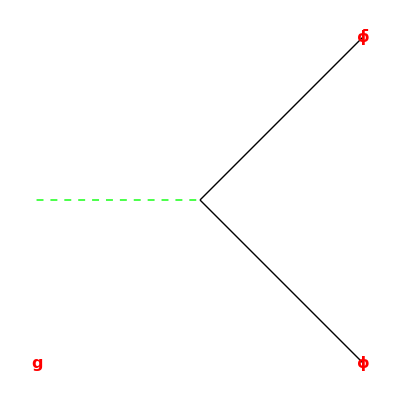
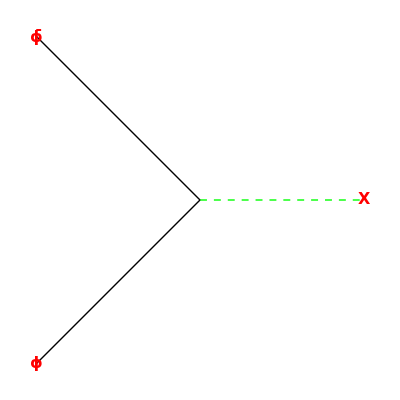
Gauge mediation: ref:Alverez-Gaume,Claudson,Wise NP B207 96(1982) {Standard SUSY} | V[ϕ.ϕ.Vector] | Messenger[ϕ+ϕ̄]
M ϕ ϕ̄ | V[X ϕ^2,adds mass] | ⟨X_F⟩.ϕ_A.ϕ_A
{SUSY breaking w/,ϕ→A+θ.ψ+θ.θ.F}
⟨F_X⟩≠0
 | -Graphics- |  |  | -Graphics-
Two fields carry gauge interation couple to X.  Then ℒ_SUSYbreaking→⟨X_F⟩ (A^2+(A^*)^2)

```mathematica
{vx,line}=GraphicPointLines[5,3,{{2,5},{5,9},{5,7},{7,11},{9,11},{11,14}}];
Linex[i_]:=Line[line[[i]]]
font:={Red,Bold,16}
PR1["Gauge mediation: ref:Alverez-Gaume,Claudson,Wise NP B207 96(1982) ",
Grid[{
{{"Standard SUSY"},V[ϕ. ϕ. "Vector"],Column[{"Messenger[ϕ+ϕ̄]",M ϕ ϕ̄},Center],V[X ϕ ϕ,"adds mass"],
Column[{BraKet[Subscript[X, F]].Subscript[ϕ, A].Subscript[ϕ, A],
{"SUSY breaking w/",ϕ->A+θ.ψ+θ.θ.F},
BraKet[Subscript[F, X]]≠0},Center]},
{,Graphics[{Thin,Black,
{Dashed,Green,Thick,Linex[1]},
Linex[2],
Linex[3],
Text[Style[ϕ,font],vx[[7]]],
Text[Style[ϕ̄,font],vx[[9]]],
Text[Style[g,font],vx[[1]]]
}],,,
Graphics[{Thin,Black,
{Dashed,Green,Thick,Linex[6]},
Linex[4],
Linex[5],
Text[Style[ϕ,font],vx[[7]]],
Text[Style[ϕ̄,font],vx[[9]]],
Text[Style[X,font],vx[[14]]]
}]
}
},Frame->All],NL,
"Two fields carry gauge interation couple to X.  Then ",Subscript[ℒ, SUSYbreaking]->BraKet[Subscript[X, F]](A^2+SuperStar[A]^2)
];
```

General graphic definitions for array points and lines.

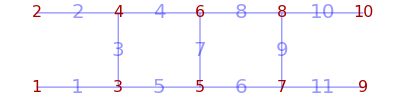

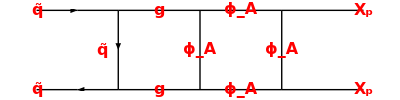

The above X_F cause δM splitting in ψψbar spectrum which would cancel with SUSY self energy diagram below.

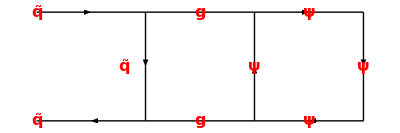

```mathematica
{vx,line}=GraphicPointLines[5,2,{{1,3},{2,4},{3,4},{4,6},{3,5},{5,7},{6,5},{6,8},{8,7},{8,10},{7,9}}];
Linex[i_]:=Line[line[[i]]]
font:={Red,Bold,16}

Graphics[{Thin,Black,
MidArrow[line[[1]]//Reverse],MidArrow[line[[2]]],MidArrow[line[[3]]//Reverse],
Linex[4],Linex[5],Linex[6],Linex[7],Linex[8],Linex[9],Linex[10],Linex[11],
Text[Style[q̃,font],vx[[1]]],
Text[Style[q̃,font],vx[[2]]],
Text[Style[Subscript[X, p],font],vx[[9]]],
Text[Style[Subscript[X, p],font],vx[[10]]],
MidLineTextOffset[q̃,line[[3]],font,{-.2,0}],
MidLineText[g,line[[4]],font],
MidLineText[g,line[[5]],font],
MidLineText[Subscript[ϕ, A],line[[6]],font],
MidLineText[Subscript[ϕ, A],line[[7]],font],
MidLineText[Subscript[ϕ, A],line[[8]],font],
MidLineText[Subscript[ϕ, A],line[[9]],font]
}
]
PR["The above X_F cause δM splitting in ψψbar spectrum which would cancel with SUSY self energy diagram below."
]
Graphics[{Thin,Black,
MidArrow[line[[1]]//Reverse],MidArrow[line[[2]]],MidArrow[line[[3]]//Reverse],
Linex[4],Linex[5],
MidArrow[line[[6]]//Reverse],MidArrow[line[[7]]//Reverse],MidArrow[line[[8]]],MidArrow[line[[9]]],
Text[Style[q̃,font],vx[[1]]],
Text[Style[q̃,font],vx[[2]]],
Text["",vx[[10]]],
MidLineTextOffset[q̃,line[[3]],font,{-.2,0}],
MidLineText[g,line[[4]],font],
MidLineText[g,line[[5]],font],
MidLineText[ψ,line[[6]],font],
MidLineText[ψ,line[[7]],font],
MidLineText[ψ,line[[8]],font],
MidLineText[ψ,line[[9]],font]
}
]
```